```mathematica
Manipulate[
Module[{vr,k,vo,ra,sol,Ca,Cb,x,profit,optimalvolume,profitPlot,concentrationPlot},
vr:=If[TrueQ[op],optimalvolume,vrpt[[1]]];
k=0.1;
vo=10;
ra[V_]:=-k*ca[V]*If[reaction==1,1,cb[V]];

sol:=If[reactor==1,
Quiet@First@Solve[V==(vo*(Ca0-ca[V]))/(-ra[V])∧V==(vo*(Cb0-cb[V]))/ra[V],{ca[V],cb[V]}],
Quiet@First@NDSolve[{ca'[V]==ra[V]/vo,cb'[V]==-ra[V]/vo,ca[0]==Ca0,cb[0]==Cb0},{ca,cb},{V,0,1000}]];

Ca[vol_]:=Evaluate[ca[V]/.sol/.V->vol];
Cb[vol_]:=Evaluate[cb[V]/.sol/.V->vol];

x[vol_]:=(Ca0-Ca[vol])/Ca0;

profit[vol_]:=If[reactor==1,vo*Ca0*x[vol],vo*Cb[vol]]*pb-vo*Ca0*pa-reactorprice*vol;

optimalvolume:=If[Sum[x[vol],{vol,1,1000}]==0,1,V/.Quiet@FindMaximum[profit[V],{V,vrpt[[1]],1,1000}][[2]]];

profitPlot:=Show[
Plot[profit[vol],{vol,0,1000},PlotStyle->{Thick,RGBColor[0.02,0.44,0.]}],
Graphics[{PointSize[0.0325],Point[{vr,profit[vr]}]}],
FrameLabel->{Style["reactor volume (L)",17],Style["profit  ($/min)",17]},
PlotRange->All,
PlotRangePadding->{{10,10},{Scaled[0.01],Scaled[0.1]}},
ImagePadding->{{75,15},{45,10}}];

concentrationPlot:=Show[
Plot[{Ca[vol],Cb[vol]},{vol,0,vr},PlotStyle->{{Thick,Blue},{Thick,Black}}],
Graphics[{
Text[Style[" reactant ",17,Blue,Background->White],{0.33*vr,Ca[0.33*vr]}],
Text[Style[" product ",17,Background->White],{0.666*vr,Cb[0.666*vr]}]
}],
FrameLabel->{Style["reactor volume (L)",17],Style["concentration  (mol/L)",17]},
PlotRange->{{0,vr},{All,All}},
ImagePadding->{{50,15},{45,10}}];

Column[{
Text@Style["reactor cannot operate under these conditions",18,If[optimalvolume==1,Black,Transparent]],
Show[Switch[plot,1,profitPlot,2,concentrationPlot],ImageSize->{400,325},AspectRatio->Full,Frame->True,LabelStyle->{Black,14},Axes->False],
Spacer[10],
Text@Style[Row[{"profit = ",If[profit[vr]<0,"-$","$"],NumberForm[Round[Abs@profit[vr]],DigitBlock->3],"/min",Spacer[25],"conversion = ",NumberForm[x[vr],{2,2}]}],18]
},Center]

],
Column[{
Style["select a plot:",Bold],
Control[{{plot,1,""},{1->"profit",2->"concentration"},RadioButton}],Spacer[0],
Style["reactor type:",Bold],
Control[{{reactor,1,""},{1->"CSTR",2->"PFR"},RadioButton}],Spacer[0],
Style["reaction:",Bold],
Control[{{reaction,1,""},{1->"first order",2->"autocatalytic"},RadioButton}]
},Left],
Delimiter,
Column[{
Style["feed concentrations (mol/L)",Bold],
Control[{{Ca0,5,"reactant"},1,5,1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{Cb0,1,"product"},0,5,1,Appearance->"Labeled",ImageSize->Tiny}]
}],
Delimiter,
PaneSelector[{
1->Column[{
Style["value and cost ($/mol)",Bold],
Control[{{pb,100,"product"},20,200,1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{pa,10,"reactant"},1,20,0.5,Appearance->"Labeled",ImageSize->Tiny}],
Style["cost ($/L/min)",Bold],
Control[{{reactorprice,5,"reactor"},1,10,1,Appearance->"Labeled",ImageSize->Tiny}],Spacer[0],
Control[{{op,False,"optimize"},{True,False}}]
}],
2->Control[{{op,False,"optimize"},{True,False}}]
},Dynamic@plot],
Control[{{vrpt,{50,0}},{1,-25000},{1000,10000},Locator,Appearance->None}],
ControlPlacement->Left]
```

```mathematica
(*If[reaction==1,
Quiet@First@Solve[V==(vo*(Ca0-ca[V]))/(-ra[V])∧V==(vo*(Cb0-cb[V]))/ra[V],{ca[V],cb[V]}],
Quiet@First@Solve[ca[V]==(vo*Ca0)/(vo+k*V*cb[V])∧cb[V]==(vo*Cb0)/(vo-k*V*ca[V]),{ca[V],cb[V]}]],*)
```

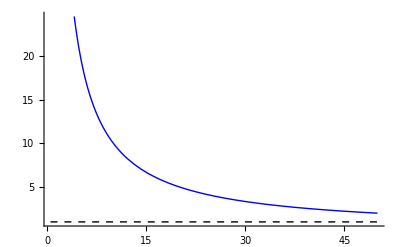

```mathematica
Module[{k,vo,τ,Ca0},
k=0.1;
vo=10;
τ:=V/vo;
Ca0=1;

Show[
Plot[((1+k*Ca0*τ)+√((1+k*Ca0*τ)^2-4*k*τ*Ca0))/(2*k*τ),{V,0,50},PlotStyle->{Thick,Blue}],
Plot[((1+k*Ca0*τ)-√((1+k*Ca0*τ)^2-4*k*τ*Ca0))/(2*k*τ),{V,0,50},PlotStyle->{Thick,Dashed,Black}],
(*Plot[((1+0.01*V*Ca0)-√((1+0.01*V*Ca0)^2-4*0.01*V*Ca0))/(2*0.01*V),{V,0,50},PlotStyle->{Thick,Dashed,Black}],*)
AxesOrigin->{0,0},PlotRange->All]
]
```